# Bistable motif: parameter sampling

## Finding the condition of multistationarity

We consider the following reactions:

K+S⇋KS→K+S_p
K^✶+S⇋K^✶S→K^✶+S_p
S_p→S
K⇋K^✶
KS⇋K^✶S

The species of the system are:

{S,S_p,K,K^✶,KS,K^✶S}

In total, there are 11 reations and 6 species.

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms]
```

-k_2^2 k_5^2 k_7 k_8 k_9-2 k_2 k_3 k_5^2 k_7 k_8 k_9-k_3^2 k_5^2 k_7 k_8 k_9-2 k_2^2 k_5 k_6 k_7 k_8 k_9-4 k_2 k_3 k_5 k_6 k_7 k_8 k_9-2 k_3^2 k_5 k_6 k_7 k_8 k_9-k_2^2 k_6^2 k_7 k_8 k_9-2 k_2 k_3 k_6^2 k_7 k_8 k_9-k_3^2 k_6^2 k_7 k_8 k_9-k_2^2 k_5^2 k_7 k_9^2-2 k_2 k_3 k_5^2 k_7 k_9^2-k_3^2 k_5^2 k_7 k_9^2-2 k_2^2 k_5 k_6 k_7 k_9^2-4 k_2 k_3 k_5 k_6 k_7 k_9^2-2 k_3^2 k_5 k_6 k_7 k_9^2-k_2^2 k_6^2 k_7 k_9^2-2 k_2 k_3 k_6^2 k_7 k_9^2-k_3^2 k_6^2 k_7 k_9^2-2 k_2 k_5^2 k_7 k_8 k_9 k_10-2 k_3 k_5^2 k_7 k_8 k_9 k_10-4 k_2 k_5 k_6 k_7 k_8 k_9 k_10-4 k_3 k_5 k_6 k_7 k_8 k_9 k_10-2 k_2 k_6^2 k_7 k_8 k_9 k_10-2 k_3 k_6^2 k_7 k_8 k_9 k_10-2 k_2 k_5^2 k_7 k_9^2 k_10-2 k_3 k_5^2 k_7 k_9^2 k_10-4 k_2 k_5 k_6 k_7 k_9^2 k_10-4 k_3 k_5 k_6 k_7 k_9^2 k_10-2 k_2 k_6^2 k_7 k_9^2 k_10-2 k_3 k_6^2 k_7 k_9^2 k_10-k_5^2 k_7 k_8 k_9 k_10^2-2 k_5 k_6 k_7 k_8 k_9 k_10^2-k_6^2 k_7 k_8 k_9 k_10^2-k_5^2 k_7 k_9^2 k_10^2-2 k_5 k_6 k_7 k_9^2 k_10^2-k_6^2 k_7 k_9^2 k_10^2-2 k_2^2 k_5 k_7 k_8 k_9 k_11-4 k_2 k_3 k_5 k_7 k_8 k_9 k_11-2 k_3^2 k_5 k_7 k_8 k_9 k_11-2 k_2^2 k_6 k_7 k_8 k_9 k_11-4 k_2 k_3 k_6 k_7 k_8 k_9 k_11-2 k_3^2 k_6 k_7 k_8 k_9 k_11-2 k_2^2 k_5 k_7 k_9^2 k_11-4 k_2 k_3 k_5 k_7 k_9^2 k_11-2 k_3^2 k_5 k_7 k_9^2 k_11-2 k_2^2 k_6 k_7 k_9^2 k_11-4 k_2 k_3 k_6 k_7 k_9^2 k_11-2 k_3^2 k_6 k_7 k_9^2 k_11-2 k_2 k_5 k_7 k_8 k_9 k_10 k_11-2 k_3 k_5 k_7 k_8 k_9 k_10 k_11-2 k_2 k_6 k_7 k_8 k_9 k_10 k_11-2 k_3 k_6 k_7 k_8 k_9 k_10 k_11-2 k_2 k_5 k_7 k_9^2 k_10 k_11-2 k_3 k_5 k_7 k_9^2 k_10 k_11-2 k_2 k_6 k_7 k_9^2 k_10 k_11-2 k_3 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_7 k_8 k_9 k_11^2-2 k_2 k_3 k_7 k_8 k_9 k_11^2-k_3^2 k_7 k_8 k_9 k_11^2-k_2^2 k_7 k_9^2 k_11^2-2 k_2 k_3 k_7 k_9^2 k_11^2-k_3^2 k_7 k_9^2 k_11^2+(-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_1^3+(-k_2^2 k_4 k_5 k_6 k_8^2-2 k_2 k_3 k_4 k_5 k_6 k_8^2-k_3^2 k_4 k_5 k_6 k_8^2-k_2^2 k_4 k_6^2 k_8^2-2 k_2 k_3 k_4 k_6^2 k_8^2-k_3^2 k_4 k_6^2 k_8^2-k_2^2 k_4 k_5 k_7 k_8^2-2 k_2 k_3 k_4 k_5 k_7 k_8^2-k_3^2 k_4 k_5 k_7 k_8^2-k_2^2 k_4 k_6 k_7 k_8^2-2 k_2 k_3 k_4 k_6 k_7 k_8^2-k_3^2 k_4 k_6 k_7 k_8^2-k_1 k_2 k_3 k_5^2 k_8 k_9-k_1 k_3^2 k_5^2 k_8 k_9-2 k_1 k_2 k_3 k_5 k_6 k_8 k_9-2 k_1 k_3^2 k_5 k_6 k_8 k_9-k_2^2 k_4 k_5 k_6 k_8 k_9-2 k_2 k_3 k_4 k_5 k_6 k_8 k_9-k_3^2 k_4 k_5 k_6 k_8 k_9-k_1 k_2 k_3 k_6^2 k_8 k_9-k_1 k_3^2 k_6^2 k_8 k_9-k_2^2 k_4 k_6^2 k_8 k_9-2 k_2 k_3 k_4 k_6^2 k_8 k_9-k_3^2 k_4 k_6^2 k_8 k_9-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_8 k_9-k_1 k_3 k_5^2 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-2 k_1 k_2 k_5 k_6 k_7 k_8 k_9-2 k_1 k_3 k_5 k_6 k_7 k_8 k_9-k_1 k_2 k_6^2 k_7 k_8 k_9-k_1 k_3 k_6^2 k_7 k_8 k_9-k_1 k_2 k_3 k_5^2 k_9^2-k_1 k_3^2 k_5^2 k_9^2-2 k_1 k_2 k_3 k_5 k_6 k_9^2-2 k_1 k_3^2 k_5 k_6 k_9^2-k_1 k_2 k_3 k_6^2 k_9^2-k_1 k_3^2 k_6^2 k_9^2-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-2 k_2 k_4 k_5 k_6 k_8^2 k_10-2 k_3 k_4 k_5 k_6 k_8^2 k_10-2 k_2 k_4 k_6^2 k_8^2 k_10-2 k_3 k_4 k_6^2 k_8^2 k_10-2 k_2 k_4 k_5 k_7 k_8^2 k_10-2 k_3 k_4 k_5 k_7 k_8^2 k_10-2 k_2 k_4 k_6 k_7 k_8^2 k_10-2 k_3 k_4 k_6 k_7 k_8^2 k_10-k_1 k_3 k_5^2 k_8 k_9 k_10-k_1 k_2 k_5 k_6 k_8 k_9 k_10-3 k_1 k_3 k_5 k_6 k_8 k_9 k_10-2 k_2 k_4 k_5 k_6 k_8 k_9 k_10-2 k_3 k_4 k_5 k_6 k_8 k_9 k_10-k_1 k_2 k_6^2 k_8 k_9 k_10-2 k_1 k_3 k_6^2 k_8 k_9 k_10-2 k_2 k_4 k_6^2 k_8 k_9 k_10-2 k_3 k_4 k_6^2 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_8 k_9 k_10-k_1 k_3 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-k_1 k_5^2 k_7 k_8 k_9 k_10-k_1 k_2 k_6 k_7 k_8 k_9 k_10-k_1 k_3 k_6 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-2 k_1 k_5 k_6 k_7 k_8 k_9 k_10-k_1 k_6^2 k_7 k_8 k_9 k_10-k_1 k_3 k_5^2 k_9^2 k_10-k_1 k_2 k_5 k_6 k_9^2 k_10-3 k_1 k_3 k_5 k_6 k_9^2 k_10-k_1 k_2 k_6^2 k_9^2 k_10-2 k_1 k_3 k_6^2 k_9^2 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_4 k_5 k_6 k_8^2 k_10^2-k_4 k_6^2 k_8^2 k_10^2-k_4 k_5 k_7 k_8^2 k_10^2-k_4 k_6 k_7 k_8^2 k_10^2-k_1 k_5 k_6 k_8 k_9 k_10^2-k_4 k_5 k_6 k_8 k_9 k_10^2-k_1 k_6^2 k_8 k_9 k_10^2-k_4 k_6^2 k_8 k_9 k_10^2-k_1 k_5 k_7 k_8 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_1 k_6 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_6 k_9^2 k_10^2-k_1 k_6^2 k_9^2 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2 k_3 k_4 k_5 k_8^2 k_11-k_3^2 k_4 k_5 k_8^2 k_11-k_2^2 k_4 k_6 k_8^2 k_11-3 k_2 k_3 k_4 k_6 k_8^2 k_11-2 k_3^2 k_4 k_6 k_8^2 k_11-k_2^2 k_4 k_7 k_8^2 k_11-2 k_2 k_3 k_4 k_7 k_8^2 k_11-k_3^2 k_4 k_7 k_8^2 k_11-k_2 k_4 k_5 k_7 k_8^2 k_11-k_3 k_4 k_5 k_7 k_8^2 k_11-k_2 k_4 k_6 k_7 k_8^2 k_11-k_3 k_4 k_6 k_7 k_8^2 k_11-2 k_1 k_2 k_3 k_5 k_8 k_9 k_11-2 k_1 k_3^2 k_5 k_8 k_9 k_11-k_2 k_3 k_4 k_5 k_8 k_9 k_11-k_3^2 k_4 k_5 k_8 k_9 k_11-2 k_1 k_2 k_3 k_6 k_8 k_9 k_11-2 k_1 k_3^2 k_6 k_8 k_9 k_11-k_2^2 k_4 k_6 k_8 k_9 k_11-3 k_2 k_3 k_4 k_6 k_8 k_9 k_11-2 k_3^2 k_4 k_6 k_8 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_8 k_9 k_11-2 k_1 k_3 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-2 k_1 k_2 k_6 k_7 k_8 k_9 k_11-2 k_1 k_3 k_6 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_3 k_5 k_9^2 k_11-2 k_1 k_3^2 k_5 k_9^2 k_11-2 k_1 k_2 k_3 k_6 k_9^2 k_11-2 k_1 k_3^2 k_6 k_9^2 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_3 k_4 k_5 k_8^2 k_10 k_11-k_2 k_4 k_6 k_8^2 k_10 k_11-2 k_3 k_4 k_6 k_8^2 k_10 k_11-k_2 k_4 k_7 k_8^2 k_10 k_11-k_3 k_4 k_7 k_8^2 k_10 k_11-k_4 k_5 k_7 k_8^2 k_10 k_11-k_4 k_6 k_7 k_8^2 k_10 k_11-k_1 k_3 k_5 k_8 k_9 k_10 k_11-k_3 k_4 k_5 k_8 k_9 k_10 k_11-k_1 k_2 k_6 k_8 k_9 k_10 k_11-2 k_1 k_3 k_6 k_8 k_9 k_10 k_11-k_2 k_4 k_6 k_8 k_9 k_10 k_11-2 k_3 k_4 k_6 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_7 k_8 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_1 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_1 k_6 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_5 k_9^2 k_10 k_11-k_1 k_2 k_6 k_9^2 k_10 k_11-2 k_1 k_3 k_6 k_9^2 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2 k_3 k_4 k_8^2 k_11^2-k_3^2 k_4 k_8^2 k_11^2-k_2 k_4 k_7 k_8^2 k_11^2-k_3 k_4 k_7 k_8^2 k_11^2-k_1 k_2 k_3 k_8 k_9 k_11^2-k_1 k_3^2 k_8 k_9 k_11^2-k_2 k_3 k_4 k_8 k_9 k_11^2-k_3^2 k_4 k_8 k_9 k_11^2-k_1 k_2 k_7 k_8 k_9 k_11^2-k_1 k_3 k_7 k_8 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_3 k_9^2 k_11^2-k_1 k_3^2 k_9^2 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2) x_3+x_1^2 (-k_1 k_2 k_4 k_5 k_7 k_9 k_10-k_1 k_3 k_4 k_5 k_7 k_9 k_10-k_1 k_2 k_4 k_6 k_7 k_9 k_10-k_1 k_3 k_4 k_6 k_7 k_9 k_10-k_1 k_4 k_5 k_7 k_9 k_10^2-k_1 k_4 k_6 k_7 k_9 k_10^2-k_2^2 k_4^2 k_7 k_8 k_11-2 k_2 k_3 k_4^2 k_7 k_8 k_11-k_3^2 k_4^2 k_7 k_8 k_11-2 k_1 k_2 k_4 k_5 k_7 k_9 k_11-2 k_1 k_3 k_4 k_5 k_7 k_9 k_11-2 k_1 k_2 k_4 k_6 k_7 k_9 k_11-2 k_1 k_3 k_4 k_6 k_7 k_9 k_11-k_1 k_2 k_4 k_5 k_7 k_10 k_11-k_1 k_3 k_4 k_5 k_7 k_10 k_11-k_1 k_2 k_4 k_6 k_7 k_10 k_11-k_1 k_3 k_4 k_6 k_7 k_10 k_11-k_2 k_4^2 k_7 k_8 k_10 k_11-k_3 k_4^2 k_7 k_8 k_10 k_11-2 k_1 k_2 k_4 k_7 k_9 k_10 k_11-2 k_1 k_3 k_4 k_7 k_9 k_10 k_11-k_1 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_4 k_6 k_7 k_9 k_10 k_11-k_2^2 k_4^2 k_7 k_11^2-2 k_2 k_3 k_4^2 k_7 k_11^2-k_3^2 k_4^2 k_7 k_11^2-k_2 k_4^2 k_7 k_8 k_11^2-k_3 k_4^2 k_7 k_8 k_11^2-2 k_1 k_2 k_4 k_7 k_9 k_11^2-2 k_1 k_3 k_4 k_7 k_9 k_11^2+(k_1^2 k_3 k_4 k_5 k_9 k_10+k_1^2 k_3 k_4 k_6 k_9 k_10-k_1^2 k_4 k_5 k_6 k_9 k_10-k_1^2 k_4 k_6^2 k_9 k_10-k_1^2 k_4 k_5 k_6 k_10^2-k_1^2 k_4 k_6^2 k_10^2-k_1^2 k_4 k_5 k_7 k_10^2-k_1^2 k_4 k_6 k_7 k_10^2-k_1 k_2 k_3 k_4^2 k_8 k_11-k_1 k_3^2 k_4^2 k_8 k_11+k_1 k_2 k_4^2 k_6 k_8 k_11+k_1 k_3 k_4^2 k_6 k_8 k_11-k_1^2 k_3 k_4 k_5 k_10 k_11-k_1^2 k_3 k_4 k_6 k_10 k_11-k_1 k_2 k_4^2 k_6 k_10 k_11-k_1 k_3 k_4^2 k_6 k_10 k_11-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1^2 k_4 k_5 k_7 k_10 k_11-k_1^2 k_4 k_6 k_7 k_10 k_11-k_1 k_2 k_3 k_4^2 k_11^2-k_1 k_3^2 k_4^2 k_11^2-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_3)+x_1 (-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-k_1 k_2 k_5^2 k_7 k_9 k_10-k_1 k_3 k_5^2 k_7 k_9 k_10-2 k_1 k_2 k_5 k_6 k_7 k_9 k_10-2 k_1 k_3 k_5 k_6 k_7 k_9 k_10-k_1 k_2 k_6^2 k_7 k_9 k_10-k_1 k_3 k_6^2 k_7 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9 k_10^2-2 k_1 k_5 k_6 k_7 k_9 k_10^2-k_1 k_6^2 k_7 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2^2 k_4 k_5 k_7 k_8 k_11-2 k_2 k_3 k_4 k_5 k_7 k_8 k_11-k_3^2 k_4 k_5 k_7 k_8 k_11-k_2^2 k_4 k_6 k_7 k_8 k_11-2 k_2 k_3 k_4 k_6 k_7 k_8 k_11-k_3^2 k_4 k_6 k_7 k_8 k_11-2 k_2^2 k_4 k_5 k_7 k_9 k_11-4 k_2 k_3 k_4 k_5 k_7 k_9 k_11-2 k_3^2 k_4 k_5 k_7 k_9 k_11-2 k_2^2 k_4 k_6 k_7 k_9 k_11-4 k_2 k_3 k_4 k_6 k_7 k_9 k_11-2 k_3^2 k_4 k_6 k_7 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_2 k_4 k_5 k_7 k_8 k_10 k_11-k_3 k_4 k_5 k_7 k_8 k_10 k_11-k_2 k_4 k_6 k_7 k_8 k_10 k_11-k_3 k_4 k_6 k_7 k_8 k_10 k_11-k_1 k_2 k_5 k_7 k_9 k_10 k_11-k_1 k_3 k_5 k_7 k_9 k_10 k_11-2 k_2 k_4 k_5 k_7 k_9 k_10 k_11-2 k_3 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_2 k_6 k_7 k_9 k_10 k_11-k_1 k_3 k_6 k_7 k_9 k_10 k_11-2 k_2 k_4 k_6 k_7 k_9 k_10 k_11-2 k_3 k_4 k_6 k_7 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_4 k_7 k_8 k_11^2-2 k_2 k_3 k_4 k_7 k_8 k_11^2-k_3^2 k_4 k_7 k_8 k_11^2-2 k_2^2 k_4 k_7 k_9 k_11^2-4 k_2 k_3 k_4 k_7 k_9 k_11^2-2 k_3^2 k_4 k_7 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2-2 (k_1 k_2 k_4 k_5 k_6 k_8 k_10+k_1 k_3 k_4 k_5 k_6 k_8 k_10+k_1 k_2 k_4 k_6^2 k_8 k_10+k_1 k_3 k_4 k_6^2 k_8 k_10+k_1 k_2 k_4 k_5 k_7 k_8 k_10+k_1 k_3 k_4 k_5 k_7 k_8 k_10+k_1 k_2 k_4 k_6 k_7 k_8 k_10+k_1 k_3 k_4 k_6 k_7 k_8 k_10+k_1 k_2 k_4 k_5 k_6 k_9 k_10+k_1 k_3 k_4 k_5 k_6 k_9 k_10+k_1 k_2 k_4 k_6^2 k_9 k_10+k_1 k_3 k_4 k_6^2 k_9 k_10+k_1 k_2 k_4 k_5 k_7 k_9 k_10+k_1 k_3 k_4 k_5 k_7 k_9 k_10+k_1 k_2 k_4 k_6 k_7 k_9 k_10+k_1 k_3 k_4 k_6 k_7 k_9 k_10+k_1 k_4 k_5 k_6 k_8 k_10^2+k_1 k_4 k_6^2 k_8 k_10^2+k_1 k_4 k_5 k_7 k_8 k_10^2+k_1 k_4 k_6 k_7 k_8 k_10^2+k_1 k_4 k_5 k_6 k_9 k_10^2+k_1 k_4 k_6^2 k_9 k_10^2+k_1 k_4 k_5 k_7 k_9 k_10^2+k_1 k_4 k_6 k_7 k_9 k_10^2+k_1 k_2 k_3 k_4 k_5 k_8 k_11+k_1 k_3^2 k_4 k_5 k_8 k_11+k_1 k_2 k_3 k_4 k_6 k_8 k_11+k_1 k_3^2 k_4 k_6 k_8 k_11+k_1 k_2 k_4 k_5 k_7 k_8 k_11+k_1 k_3 k_4 k_5 k_7 k_8 k_11+k_1 k_2 k_4 k_6 k_7 k_8 k_11+k_1 k_3 k_4 k_6 k_7 k_8 k_11+k_1 k_2 k_3 k_4 k_5 k_9 k_11+k_1 k_3^2 k_4 k_5 k_9 k_11+k_1 k_2 k_3 k_4 k_6 k_9 k_11+k_1 k_3^2 k_4 k_6 k_9 k_11+k_1 k_2 k_4 k_5 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_7 k_9 k_11+k_1 k_2 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_8 k_10 k_11+k_1 k_2 k_4 k_6 k_8 k_10 k_11+2 k_1 k_3 k_4 k_6 k_8 k_10 k_11+k_1 k_2 k_4 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_7 k_8 k_10 k_11+k_1 k_4 k_5 k_7 k_8 k_10 k_11+k_1 k_4 k_6 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_5 k_9 k_10 k_11+k_1 k_2 k_4 k_6 k_9 k_10 k_11+2 k_1 k_3 k_4 k_6 k_9 k_10 k_11+k_1 k_2 k_4 k_7 k_9 k_10 k_11+k_1 k_3 k_4 k_7 k_9 k_10 k_11+k_1 k_4 k_5 k_7 k_9 k_10 k_11+k_1 k_4 k_6 k_7 k_9 k_10 k_11+k_1 k_2 k_3 k_4 k_8 k_11^2+k_1 k_3^2 k_4 k_8 k_11^2+k_1 k_2 k_4 k_7 k_8 k_11^2+k_1 k_3 k_4 k_7 k_8 k_11^2+k_1 k_2 k_3 k_4 k_9 k_11^2+k_1 k_3^2 k_4 k_9 k_11^2+k_1 k_2 k_4 k_7 k_9 k_11^2+k_1 k_3 k_4 k_7 k_9 k_11^2) x_3)

```mathematica
factor=Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
Factor[factor]
```

k_1 k_4 (k_1 k_3 k_5 k_9 k_10+k_1 k_3 k_6 k_9 k_10-k_1 k_5 k_6 k_9 k_10-k_1 k_6^2 k_9 k_10-k_1 k_5 k_6 k_10^2-k_1 k_6^2 k_10^2-k_1 k_5 k_7 k_10^2-k_1 k_6 k_7 k_10^2-k_2 k_3 k_4 k_8 k_11-k_3^2 k_4 k_8 k_11+k_2 k_4 k_6 k_8 k_11+k_3 k_4 k_6 k_8 k_11-k_1 k_3 k_5 k_10 k_11-k_1 k_3 k_6 k_10 k_11-k_2 k_4 k_6 k_10 k_11-k_3 k_4 k_6 k_10 k_11-k_2 k_4 k_7 k_10 k_11-k_3 k_4 k_7 k_10 k_11-k_1 k_5 k_7 k_10 k_11-k_1 k_6 k_7 k_10 k_11-k_2 k_3 k_4 k_11^2-k_3^2 k_4 k_11^2-k_2 k_4 k_7 k_11^2-k_3 k_4 k_7 k_11^2)

```mathematica
term=Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
simpTerm=FullSimplify[term]
```

-(k_2+k_3) k_4 k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11))-k_1 (k_5+k_6) k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11))

```mathematica
simplerTerm=Distribute[simpTerm/(Subscript[k, 1]*Subscript[k, 4])]/.{(Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1]-> Subscript[M, 1],(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]-> Subscript[M, 2]}
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2

This above term larger than 0 should be the necessary condition.

```mathematica
condition=simplerTerm>0
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2>0

By mannual simplying the term, we can have:

```mathematica
simpleCond=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])>(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))
```

(k_3-k_6) (-k_8 k_11 M_1+k_9 k_10 M_2)>(k_6 k_10+k_3 k_11+k_7 (k_10+k_11)) (k_11 M_1+k_10 M_2)

```mathematica
left=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)

```mathematica
right=(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

To fullfile the assumption of thermodynamic conditions for the reversible reactions, we have the the constraint:
(k_1 k_10)/(k_2 k_11)=(k_4 k_8)/(k_5 k_9).
This will give us a even simple condition. Then we will example how will this condition result in the parameter space for multistationarity.

```mathematica
oriCond=simpleCond/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

```mathematica
Simplify[oriCond,Assumptions->(Subscript[k, 1] Subscript[k, 10])/(Subscript[k, 2] Subscript[k, 11])==(Subscript[k, 4] Subscript[k, 8])/(Subscript[k, 5] Subscript[k, 9])]
```

((k_3-k_6) (k_1 k_6 k_9 k_10-k_3 k_4 k_8 k_11))/(k_1 k_4)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Better to do it manually, then we have the condition with thermodynamic constraint:

```mathematica
thermoCond=(Subscript[k, 3]-Subscript[k, 6])(Subscript[k, 6] Subscript[k, 2]-Subscript[k, 3] Subscript[k, 5])>(Subscript[k, 2]/Subscript[k, 9]×(Subscript[k, 5]^2 +Subscript[k, 6])/Subscript[k, 5]+Subscript[k, 5]/Subscript[k, 8]×(Subscript[k, 2]^2+Subscript[k, 3])/Subscript[k, 2])((Subscript[k, 6]+Subscript[k, 7]) Subscript[k, 10]+(Subscript[k, 3]+Subscript[k, 7]) Subscript[k, 11])
```

(k_3-k_6) (-k_3 k_5+k_2 k_6)>(((k_2^2+k_3) k_5)/(k_2 k_8)+(k_2 (k_5^2+k_6))/(k_5 k_9)) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Fromt the above condition, we can get some general idea that in order to satisfy the thermodynamic condition we should have:
Necessarily:
k_3>k_6 and k_2>k_5
or
k_3<k_6 and k_5>k_2
With additional (sufficiently):
k_8,k_9≫k_10,k_11 and k_7,k_10,k_11≈0

## Sampling the parameters

Here we try to sampling the parameters by enforcing the thermodynamc constraint. The parameters are sampled in biologically meaningful ranges.

```mathematica
ClearAll["Global`*"];
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms];
(*The above code is the same as first section*)


bistableKs={};
bistableParSets={};
SeedRandom[];
Timing[
Do[{
gamma=RandomVariate[GammaDistribution[7,2]];
rand13=RandomVariate[DirichletDistribution[{1,1,1,1}]];
rand11=1-Total@rand13;
rand23=RandomVariate[DirichletDistribution[{1,1,1,1}]];
rand21=1-Total@rand23;
k1=Exp[-gamma*rand13[[1]]]*1.*^3;k2=Exp[-gamma*rand23[[3]]]*1.*^3;k3=10^(RandomReal[]*6-3);k4=Exp[-gamma*rand23[[1]]]*1.*^3;k5=Exp[-gamma*rand13[[3]]]*1.*^3;k6=10^(RandomReal[]*6-3);k7=10^(RandomReal[]*6-3);
k8=Exp[-gamma*rand23[[2]]]*1.*^3;
k9=Exp[-gamma*rand11]*1.*^3;
k10=Exp[-gamma*rand13[[2]]]*1.*^3;
k11=Exp[-gamma*rand21]*1.*^3;
left=(k3-k6) (((k5+k6) k9 k10)/k4-((k2+k3) k8 k11)/k1);right=(((k5+k6) k10)/k4+((k2+k3) k11)/k1) (k6 k10+k3 k11+k7 (k10+k11));If[left>right,{
AppendTo[bistableKs,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,left,right}];
counter=1;hitQ=0;
While[hitQ==0&&counter≤10,{
x1=10^(RandomReal[]*4-3);
finalSol=NSolve[finalSubs==0/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1},{Subscript[x, 3]}];
x3=Subscript[x, 3]/.finalSol[[1]];
realSol=solution/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1,Subscript[x, 3]->x3};
T1=(Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
T2=(Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
If[0.001≤T1≤10&&0.001≤T2≤10,{
AppendTo[bistableParSets,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,T1,T2,left,right}];
hitQ=1;
}];
counter++;
}];
}];
},{i,100000}];
]
```

{157.166,Null}

```mathematica
Length[bistableParSets]
```

12

```mathematica
InputForm[bistableParSets]
```

{{50.90439070418801, 0.028718613690480965, 0.3068427897978065, 659.0618207749684, 445.3758951218196, 498.77257461166704, 
  0.21436005307652287, 30.394489741469116, 21.02817929070236, 0.33690968793422454, 279.1982166547539, 7.977432717668331, 
  1.1969874016152342, 22825.288908026487, 728.6050297478147}, {679.4372945411751, 0.0001453203886903504, 0.04902263151476019, 
  783.3194921286299, 242.97670947758425, 428.7074531754404, 0.0016923141869511112, 78.86319560255062, 3.6183076448945535, 
  0.0003997534998159097, 26.599405914052166, 2.753431754654508, 0.02285247013088493, 64.53977783097473, 0.003447682218332277}, 
 {617.6321718615675, 151.55087404662407, 70.20800131872144, 486.5797167304149, 0.05925861944582936, 0.10647023148325085, 
  0.0012125269266066976, 24.181267538134783, 159.93118757399395, 21.022760147286302, 0.0690101272382998, 6.439755445445032, 
  0.01799010246272088, 38.2755750055519, 0.2270466852032812}, {69.54381698965679, 0.6762420038315204, 194.61312343318136, 
  80.25476489108269, 0.00001806636921517055, 1.699873012204107, 0.4824208688419963, 0.1754800952252144, 6.3733508965739265, 
  0.879430672268399, 0.0007394316108171928, 9.74390579441962, 0.3386863430165946, 22.832148238939066, 0.04272100344960559}, 
 {703.4170078085631, 42.36597363572716, 284.6816803945406, 188.968208617034, 2.1742797560048102*^-6, 0.004640401615914975, 
  0.011340857854414254, 4.3771979289030565, 25.417037193452682, 299.77895354034143, 0.0003325463826825486, 0.9624896685003779, 
  0.5396661486825919, 53.09771106845904, 0.036737107385188095}, {979.7245722720811, 0.000027282112644167384, 
  0.09951027349839185, 32.75674764434066, 64.837387017668, 999.0281406246265, 0.9246055376910682, 106.83193586763706, 
  0.02019098800477218, 0.007891225421599445, 106.01117653635968, 6.586312898059927, 4.527982443168004, 1144.2281407441255, 
  31.101395693003564}, {525.5083324604483, 0.009924020938559146, 0.6317204552762933, 838.7464541619465, 55.65435082974657, 
  64.66837793550293, 0.34014807492173443, 132.05873520210042, 6.718830193633588, 0.5232932387987298, 93.5474630245058, 
  5.068080484149474, 1.0725149305630495, 933.6246765563257, 23.648886119572175}, 
 {427.54141157488556, 541.8011413047691, 341.43799750641296, 338.46568478004974, 0.000017284719501080134, 
  0.001140514479074425, 0.0029711338357161126, 1.4098787070879293, 223.49164235095387, 1.0309581595307022, 
  6.585769682801655*^-6, 8.351539840149266, 0.3679828488829228, 0.262561564759919, 1.1114460858598318*^-7}, 
 {20.485990782713486, 0.0006181184811599366, 3.8031527821932705, 689.9654487139297, 90.8752846505879, 449.53341375510536, 
  0.36423513532193247, 13.355699252921452, 1.1177004948191878, 0.22609550860670433, 82.59512839876912, 7.058318767361364, 
  0.19383612540394715, 91207.52672323365, 6917.680888923205}, {587.7584658556641, 251.56776513736773, 654.511736799559, 
  159.00627192338655, 0.0007411610271699151, 5.133175541916163, 0.001870252907091001, 10.684957600024786, 26.027755705853444, 
  632.4047698006577, 0.01677649672986746, 6.106347759939259, 0.0017329694928751688, 344935.974720034, 66616.97044729842}, 
 {803.2074827090598, 12.4259254701516, 32.01856239359477, 258.98896537159794, 0.0003710472370151985, 1.7788365960596961, 
  0.0010994122146288146, 2.5073682231978065, 402.8395726725495, 5.710183739092212, 0.08495932133907036, 7.1397572812566725, 
  0.0010053172208667252, 477.5087827010476, 0.5659876652458165}, {803.496802167425, 0.007688014439132029, 1.6181345308481425, 
  316.52713839124857, 576.2787644505061, 417.12086528259414, 0.02517520285358104, 110.5553939466, 15.99196338630873, 
  0.03144084134459237, 865.3815596882092, 7.688534174933779, 0.10180798597015503, 79780.32979794662, 2654.724141638036}}

```mathematica
transposedBiKs=Transpose[bistableParSets];biParK1=(transposedBiKs[[1]]*transposedBiKs[[10]])/(transposedBiKs[[2]]*transposedBiKs[[11]]);biParK2=(transposedBiKs[[4]]*transposedBiKs[[8]])/(transposedBiKs[[5]]*transposedBiKs[[9]]);
```

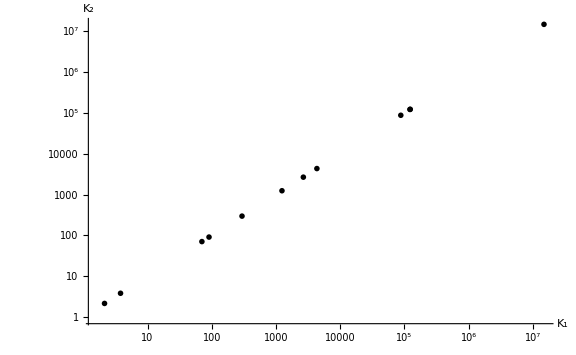

```mathematica
biPlot=ListLogLogPlot[Transpose[{biParK1,biParK2}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Monochrome"]
```

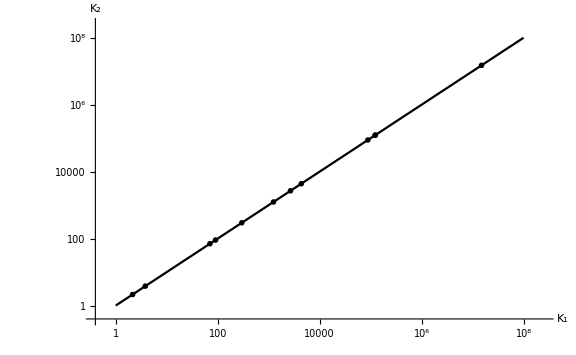

```mathematica
Show[LogLogPlot[x,{x,10^(0),10^8},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->Automatic,TicksStyle->Directive["Label", 14],AxesStyle-> Thick],biPlot]
```

```mathematica
Length[bistableKs]
```

1924

```mathematica
transposedKs=Transpose[bistableKs];parK1=(transposedKs[[1]]*transposedKs[[10]])/(transposedKs[[2]]*transposedKs[[11]]);parK2=(transposedKs[[4]]*transposedKs[[8]])/(transposedKs[[5]]*transposedKs[[9]]);
```

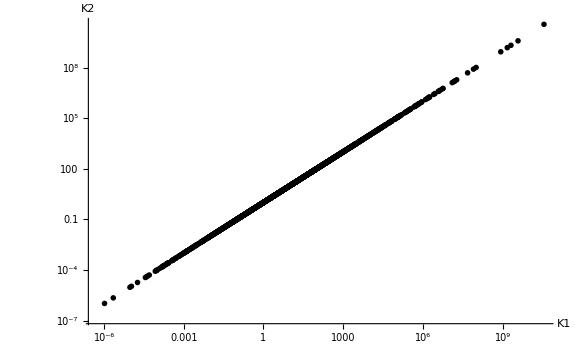

```mathematica
plot=ListLogLogPlot[Transpose[{parK1,parK2}],AxesLabel->{"K1","K2"},ImageSize->Large,PlotRange->Full,LabelStyle->{32,GrayLevel[0]},AxesStyle-> Thick,Ticks->Automatic,TicksStyle->Directive["Label", 20], PlotTheme->"Monochrome"]
```

These above results show that the parameter set within biological meaningful ranges can be reached by increasing the sampling size even when enforcing the thermodynamic constraint. Comparing to results from the other document (without enforcing thermodynamic constraint), the paramter space is largely reduced. 

□ | with thermo | with thermo | without thermo | without thermo
Sampling size | only check bistability | bistability & concentrations | only check bistability | bistability & concentrations
10^5 | 1924 | 12 | 14502 | 185
10^6 | □ | □ | □ | □